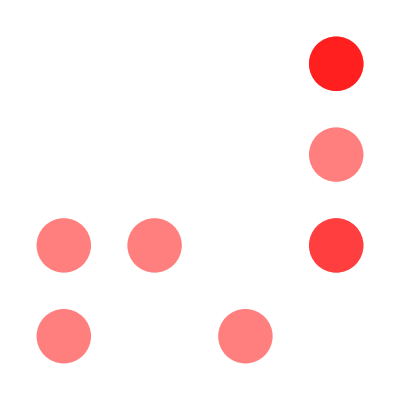

```mathematica
randCoor[]:=RandomInteger[{1,4},2]
coords=Table[randCoor[],{i,1,10}];

Options[malujKruhy]={barva->Blue, r->5}~Union~Options[Graphics];
malujKruhy[coords_,opts:OptionsPattern[]]:=Graphics[{OptionValue[barva],Opacity[0.5],Disk[#,OptionValue[r]]&/@coords},FilterRules[{opts},Options[Graphics]]]
malujKruhy[coords,"r"->.3,"barva"->Red,PlotRange->Automatic]
```

obrazek::spatnaSirka: Šířka blbě! List neni cislo

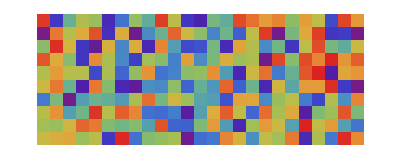

```mathematica
obrazek::spatnaSirka="Šířka blbě! `1` neni cislo";
obrazek[sirka_]:=If[NumericQ[sirka],ArrayPlot[RandomReal[1,{10,sirka}], ColorFunction->"Rainbow"],Message[obrazek::spatnaSirka, sirka]]
obrazek[List]
obrazek[25]
```

```mathematica
Messages[obrazek]
```

{HoldPattern[obrazek::spatnaSirka]:>Šířka blbě! `1` neni cislo,HoldPattern[obrazek::spatnaSrika]:>Šířka blbě!}

```mathematica
(*Contexts & packages: *)
Context[] 
Contexts["Intern*"]
BeginPackage["name`"]
```

Global`

{Internal`,Internal`ProcessEquations`}